```mathematica
L[k_,s_]=Which[k^2-4 s^2≥0,0,k^2-4 s^2<0,I 0.5  Sqrt[k^2-4 s^2]];ContourPlot[L[k,s],{s,-5,5},{k,-10,10},FrameLabel->{s,k},ColorFunction->Hue,Contours->500,PlotRange->{-5,5},PlotLegends->Automatic,ContourStyle->None]
```

-Graphics-

```mathematica
G[k_,s_]=Which[k^2-4 s^2≥0,0,k^2-4 s^2<0,I 0.5  k Sqrt[k^2-4 s^2]];ContourPlot[G[k,s],{s,-5,5},{k,-10,10},FrameLabel->{s,k},Contours->1000,PlotRange->{-25,25},ColorFunction->Hue,ContourStyle->None]
```

-Graphics-

```mathematica
u[z_,t_]=Exp[I s^2 z](s-2((b^2-s^2)Cos[2 b z √(b^2-s^2)]+I b √(b^2-s^2)Sin[2 b z √(b^2-s^2)])/(b Cosh[2t √(b^2-s^2)]-s Cos[2 b z √(b^2-s^2)]))
```

ⅇ^(ⅈ s^2 z) (s-(2 ((b^2-s^2) Cos[2 b √(b^2-s^2) z]+ⅈ b √(b^2-s^2) Sin[2 b √(b^2-s^2) z]))/(-s Cos[2 b √(b^2-s^2) z]+b Cosh[2 √(b^2-s^2) t]))

```mathematica
fpert[z_,t_]=-2Exp[I s^2 z]((b^2-s^2)Cos[2 b z √(b^2-s^2)]+I b √(b^2-s^2)Sin[2 b z √(b^2-s^2)])/(b Cosh[2t √(b^2-s^2)]-s Cos[2 b z √(b^2-s^2)])
```

-(2 ⅇ^(ⅈ s^2 z) ((b^2-s^2) Cos[2 b √(b^2-s^2) z]+ⅈ b √(b^2-s^2) Sin[2 b √(b^2-s^2) z]))/(-s Cos[2 b √(b^2-s^2) z]+b Cosh[2 √(b^2-s^2) t])

```mathematica
|b|>|s|,s≠ 0 ,KM Soliton
```

```mathematica
b=2;s=1;Plot3D[Abs[u[z,t]],{t,-2,2},{z,-2.3,2.3},PlotRange->{0,5},ColorFunction->Hue,Boxed->False,PlotPoints->100,AxesLabel->{t,z,"|u|"},LabelStyle->{FontWeight->"Bold",FontSize->18},MeshStyle->None,Ticks->{{-1.5,1.5},{-2,2},{0,5}},AxesEdge->{{-1,-1},{1,-1},{-1,-1}}]
```

-Graphics3D-

```mathematica
** 解析解
```

```mathematica
%效率非常低
```

```mathematica
uf[z,k]=FourierTransform[u[z,t],t,k]
```

$Aborted

```mathematica
** 硬数值
```

```mathematica
%k和z应该互换，Table数据以第一个范围为传播轴，ListPlot以第二个为传播轴
```

```mathematica
ListPlot3D[Table[Abs[NIntegrate[fpert[z,t] Exp[-I k t] ,{t,-5000,5000}]//N],{k,-5,5,0.2},{z,-5,5,0.2}],Boxed->False,ColorFunction->Hue,PlotRange->{0,5},DataRange->{{-5,5},{-5,5}},AxesLabel->{k,z,"|u|"},Ticks->{{-3,3},{-3,3},{0,3}},Method->{"DoubleExponentialOscillatory"}]
```

NIntegrate::ncvb: 在接近 {t} = {-9.76563} 处的 t 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.109248  + 0.270415\ ⅈ 和 0.0190217.

NIntegrate::ncvb: 在接近 {t} = {0.} 处的 t 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.493558 + 0.172725\ ⅈ 和 0.0511287.

NIntegrate::ncvb: 在接近 {t} = {0.} 处的 t 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.497664 - 1.1753\ ⅈ 和 0.1529.

General::stop: 在本次计算中，NIntegrate :: ncvb 的进一步输出将被抑制.

$Aborted

```mathematica
** 差数值算法
```

```mathematica
fplike[z_,t_]=-1/b 4 ⅇ^(ⅈ s^2 z) ((b^2-s^2) Cos[2 b √(b^2-s^2) z]+ⅈ b √(b^2-s^2) Sin[2 b √(b^2-s^2) z])Exp[-2 √(b^2-s^2) Abs[t]]
```

-1/b 4 ⅇ^(ⅈ s^2 z-2 √(b^2-s^2) Abs[t]) ((b^2-s^2) Cos[2 b √(b^2-s^2) z]+ⅈ b √(b^2-s^2) Sin[2 b √(b^2-s^2) z])

```mathematica
ListPlot3D[Table[Abs[NIntegrate[fplike[z,t]Exp[-I k t],{t,-Infinity,Infinity}]]-Abs[NIntegrate[fplike[z,t]Exp[-I k t],{t,-10,10}]]+Abs[NIntegrate[fpert[z,t]Exp[-I k t],{t,-10,10}]],{z,-5,5,0.2},{k,-5,5,0.2}],Boxed->False,ColorFunction->Hue,PlotRange->{0,5},DataRange->{{-5,5},{-5,5}},AxesLabel->{k,z,"|u|"},Ticks->{{-3,3},{-3,3},{0,3}}]
```

-Graphics3D-

```mathematica
s=0,亮孤子
```

```mathematica
b=2;s=0;Plot3D[Abs[u[z,t]],{t,-2,2},{z,-2.3,2.3},PlotRange->{0,5},ColorFunction->Hue,Boxed->False,PlotPoints->100,AxesLabel->{t,z,"|u|"},LabelStyle->{FontWeight->"Bold",FontSize->18},MeshStyle->None,Ticks->{{-1.5,1.5},{-2,2},{0,5}},AxesEdge->{{-1,-1},{1,-1},{-1,-1}}]
```

-Graphics3D-

```mathematica
uf[z_,k_]=FourierTransform[fpert[z,t],t,k]
```

-1/4 √(π/2) Sech[(k π)/8] (4 Cos[8 z]+4 ⅈ Sin[8 z])

```mathematica
Plot3D[Abs[uf[z,k]],{k,-20,20},{z,-10,10},PlotRange->{0,2},ColorFunction->Hue,Boxed->False,PlotPoints->100,AxesLabel->{k,z,"|u|"},LabelStyle->{FontWeight->"Bold",FontSize->18},MeshStyle->None,Ticks->{{-15,15},{-8,8},{0,1}},AxesEdge->{{-1,-1},{1,-1},{-1,-1}}]
```

-Graphics3D-

```mathematica
|b|<|s|,s≠ 0 ,AB Soliton
```

```mathematica
b=1;s=2;Plot3D[Abs[u[z,t]],{t,-5,5},{z,-2,2},PlotRange->{0,4},ColorFunction->Hue,Boxed->False,PlotPoints->100,AxesLabel->{t,z,"|u|"},LabelStyle->{FontWeight->"Bold",FontSize->18},MeshStyle->None,Ticks->{{-3,3},{-1.5,1.5},{0,4}},AxesEdge->{{-1,-1},{1,-1},{-1,-1}}]
```

-Graphics3D-

```mathematica
重定义
```

```mathematica
ABu[z_,t_]=Exp[I s^2 z](s-2((b^2-s^2)Cosh[2 b z √(s^2-b^2)]-I b √(s^2-b^2)Sinh[2 b z √(s^2-b^2)])/(b Cos[2t √(s^2-b^2)]-s Cosh[2 b z √(s^2-b^2)]))
```

ⅇ^(ⅈ s^2 z) (s-(2 ((b^2-s^2) Cosh[2 b √(-b^2+s^2) z]-ⅈ b √(-b^2+s^2) Sinh[2 b √(-b^2+s^2) z]))/(b Cos[2 √(-b^2+s^2) t]-s Cosh[2 b √(-b^2+s^2) z]))

```mathematica
ABfpert[z_,t_]= -2 ((b^2-s^2) Cosh[2 b z √(s^2-b^2)]-I b √(s^2-b^2) Sinh[2 b z √(s^2-b^2)])/(b Cos[2 t √(s^2-b^2)]-s Cosh[2 b z √(s^2-b^2)])Exp[I s^2 z]
```

-(2 ⅇ^(4 ⅈ z) (-3 Cosh[2 √3 z]-ⅈ √3 Sinh[2 √3 z]))/(Cos[2 √3 t]-2 Cosh[2 √3 z])

```mathematica
b=1;s=2;Plot3D[Abs[ABu[z,t]],{t,-5,5},{z,-2,2},PlotRange->{0,4},ColorFunction->Hue,Boxed->False,PlotPoints->100,AxesLabel->{t,z,"|u|"},LabelStyle->{FontWeight->"Bold",FontSize->18},MeshStyle->None,Ticks->{{-3,3},{-1.5,1.5},{0,4}},AxesEdge->{{-1,-1},{1,-1},{-1,-1}}]
```

-Graphics3D-

```mathematica
增长率比较
```

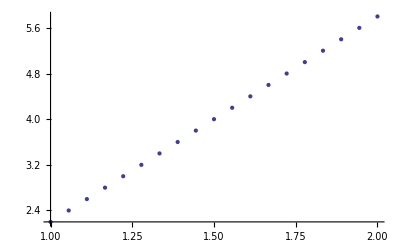

```mathematica
ListPlot[Table[Abs[ABu[0,0]],{b,0.1,1.9,0.1}],DataRange->{1,2}]
```

```mathematica
切片频谱
```

```mathematica
ABfpert[0,t]
```

6/(-2+Cos[2 √3 t])

```mathematica
FourierTransform[6/Cos[2 √3 t],t,k]
```

FourierTransform[6 Sec[2 √3 t],t,k]

```mathematica
b=s,s≠ 0 ,Rogue Wave
```

```mathematica
RWu[z_,t_]=s(1-(1+2 I s^2 z)/(0.25+s^2 t^2+s^4 z^2))Exp[I s^2 z]
```

ⅇ^(ⅈ s^2 z) s (1-(1+2 ⅈ s^2 z)/(0.25+s^2 t^2+s^4 z^2))

```mathematica
s=1;Plot3D[Abs[RWu[z,t]],{t,-2,2},{z,-2,2},PlotRange->{0,3},ColorFunction->Hue,Boxed->False,PlotPoints->100,AxesLabel->{t,z,"|u|"},LabelStyle->{FontWeight->"Bold",FontSize->18},MeshStyle->None,Ticks->{{-3,3},{-1.5,1.5},{0,4}},AxesEdge->{{-1,-1},{1,-1},{-1,-1}}]
```

-Graphics3D-

```mathematica
RWfpert[z_,t_]=-(1+2 I s^2 z)/(0.25+s^2 t^2+s^4 z^2)s Exp[I s^2 z]
```

-(ⅇ^(ⅈ z) (1+2 ⅈ z))/(0.25+t^2+z^2)

```mathematica
uf[z_,k_]=FourierTransform[RWfpert[z,t],t,k]
```

-(1.2533141373155 ⅇ^(ⅈ z-k √(0.25+z^2) Sign[k]) (1+2 ⅈ z) √(1/(0.25+z^2)) (0.25+z^2)^(1/4) √Abs[k])/(√(k √(0.25+z^2) Sign[k]))

```mathematica
Plot3D[Abs[uf[z,k]],{k,-10,10},{z,-10,10},PlotRange->{0,4},ColorFunction->Hue,Boxed->False,PlotPoints->150,AxesLabel->{k,z,"|u|"},LabelStyle->{FontWeight->"Bold",FontSize->18},MeshStyle->None,Ticks->{{-5,5},{-8,8},{0,4}},AxesEdge->{{-1,-1},{1,-1},{-1,-1}}]
```

-Graphics3D-